```mathematica
(** Set the directory that you want your plots to go to here **)
SetDirectory["/users/maxzweig/energythrust"]
```

/Users/maxzweig/energythrust

```mathematica
(** Various helper functions for standard parts of the paper / reachable set results **)
CW[n_] := {{0, 0, 0,1, 0, 0}, {0, 0, 0,0,1, 0}, {0, 0, 0, 0 ,0, 1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0, 0}, {0, 0, -n^2, 0, 0,0}} ;
cmat[ab_, tau_, tf_] := MatrixExp[-(tau - tf) ab // Transpose][[4;;6, 1;;3]];
xrf[tf_, delta_, h_, deltaT_, A_, n_, Rr_, emax_] := NIntegrate[  emax (cmat[A, tau, tf] // Transpose).cmat[A, tau, tf].delta / (deltaT.(cmat[A, tau, tf] // Transpose).cmat[A, tau, tf].delta // Sqrt)[[1]]  ,{tau, 0, tf}];
x3fanalytical[tf_, h_, n_]:= h(2Floor[n tf / Pi]+1+ Mod[Floor[n tf / Pi], 2] Cos[n tf] - (Mod[Floor[n tf / Pi], 2] - 1)(- Cos[n tf]));
```

```mathematica
(** Computes the thrust-limited reachable set for a given final time **)
thrustreachable[xrf_,tf_, na_, emax_] := Module[{points, tfs, hs, As, ns, Rrs, pointsT, rd, rdpoints, rdboundary, first2},
points = CirclePoints[1000];
points = Append[#, 0] & /@ points;
points //  N;
points[[1]];
tfs = ConstantArray[tf, 1000];
tfs[[1]];
hs = ConstantArray[1, 1000];
hs[[1]];
As = ConstantArray[CW[na], 1000];
As[[1]] // MatrixForm;
ns = ConstantArray[na, 1000];
ns[[1]];
Rrs = ConstantArray[1, 1000];
Rrs[[1]];
emaxs = ConstantArray[emax, 1000];
columntorow[x_] := {x};
pointsT = columntorow /@ points;
pointsT[[1]] // MatrixForm;
rd = MapThread[xrf, {tfs, points, hs, pointsT, As, ns, Rrs, emaxs}];
rdpoints = Map[Re, rd, {2}];
rdboundary = PolygonCoordinates[ConvexHullRegion[rdpoints]];
first2[x_] := {x[[1]], x[[2]]};
(* rboundary = Map[first2, rdboundary];*)
rdboundary
]
```

```mathematica
(** Computes the energy reachable quadratic form for an associated n and final time **)
energyform[tff_, na_] := Module[{c, r, sig, gamma, nmat},
c[n_] = {
{0, -2* n, 0, 1, 0, 0},
{2 * n, 0, 0, 0, 1, 0},
{0, 0, 0, 0,0 , 1},
{-1, 0, 0, 0, 0, 0},
{0, -1, 0, 0,0,0 }, 
{0, 0, -1, 0, 0, 0 }
}; (*Good*)
c[n] // MatrixForm;
r[t_, n_] = {{72  * t  * Cos[n * t] + (154 * n * t + 48 * n ^ 3 * t ^ 3 - 384 * Sin[n * t] - 27 * Sin[2 * n * t]) / (4 * n), -3 * n * t ^ 2 + (6 - 6 * Cos[n * t] ) / n, 0, (8+12 * n^2* t^2−8* Cos[n * t]−24*n* t* Sin[n * t]+9 *Sin[ n * t]^2 )/ (2 * n ^ 2), (23 *n * t+6 *n^3 *t^3+42*n*t* Cos[ n * t]−56 * Sin[ n * t]−(9/2) * Sin [2*n*t])/n^2, 0
},
{-3 * n * t ^ 2 + (6 - 6 * Cos[n * t] ) / n, t, 0,  (-2*n * t + 2 * Sin[n * t]) / n^2, - 3 * t^2 / 2 + (4 - 4 Cos[n * t])/n ^ 2, 0 
},
{
0, 0, ( 2 * n * t + Sin[2 * n * t]) / (4 *n) , 0, 0, Sin[n * t] ^ 2 / (2 * n^2)
},
{(8+12 * n^2* t^2−8* Cos[n * t]−24*n* t* Sin[n * t]+9 *Sin[ n * t]^2 )/ (2 * n ^ 2), (-2*n * t + 2 * Sin[n * t]) / n^2, 0, (26 * n * t - 32 * Sin[n * t] + 3 * Sin[2 * n * t]) / (4 * n^3), 3 * (- n * t + Sin[n * t])^2/ n ^ 3, 0
},
{(23 *n * t+6 *n^3 *t^3+42*n*t* Cos[ n * t]−56 * Sin[ n * t]−(9/2) * Sin [2*n*t])/n^2, - 3 * t^2 / 2 + (4 - 4 Cos[n * t])/n ^ 2, 0, 3* (-n *t + Sin[n * t])^2 / n^3,(14 * n * t + 3 * n^3 * t^3 + 24 * n * t * Cos[n * t] - 32 * Sin[n * t] - 3 * Sin[ 2 *n *t]) / n ^3 , 0 
}, 
{0, 0,  Sin[n * t] ^ 2 / (2 * n^2), 0, 0, (2 * n * t - Sin[2 * n *t ]) / (4 * n^3)
}
};(*Good*)
r[t, n] // MatrixForm;
sig[t_, n_] = {{4-3 Cos[n t],0,0,Sin[n t]/n,(2-2 Cos[n t])/n,0},{6 (-n t+Sin[n t]),1,0,(2 (-1+Cos[n t]))/n,-3 t+(4 Sin[n t])/n,0},{0,0,Cos[n t],0,0,Sin[n t]/n},{3 n Sin[n t],0,0,Cos[n t],2 Sin[n t],0},{6 n (-1+Cos[n t]),0,0,-2 Sin[n t],-3+4 Cos[n t],0},{0,0,-n Sin[n t],0,0,Cos[n t]}}; (* Good *)
gamma[t_, t0_, n_] = sig[t, n]. (sig[t0, n] // Inverse);

nmat[t0_, tf_, n_] = (Join[sig[t0, n] // Inverse, - sig[tf, n] // Inverse, 2] // Transpose). (c[n] // Transpose). (r[tf, n] // Inverse).c[n].Join[sig[t0, n] // Inverse, - sig[tf, n] // Inverse, 2];
nmat[0, tff, na]
]
```

```mathematica
(** Given points on the boundary of the thrust limited reachable set, and given the associated energy-quadratic form, computes min and max ratios, as well as the angles at which these ratios occur **)
reachablestatsoperator[b_, points_, em_] := Module[{rats, vecs}, 
ratio[pos_, quad_]:= ((em *(Eigenvalues[{Join[Join[({pos // Normalize} // Transpose).{pos // Normalize}, {{0,0,0}, {0,0,0}, {0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}])[[1]]) // Sqrt) / Norm[pos];
maxminrat[a_, v1s_] := {MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}] // Max,   MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}] // Min };
maxminvec[a_, v1s_] := {v1s[[  Position[MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}], MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}] // Max    ][[1, 1]] ]], v1s[[  Position[MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}], MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}] // Min    ][[1, 1]] ]]};
rats = maxminrat[b, points];
vecs = maxminvec[b, points];
{rats , {vecs[[1, 1;;2]], vecs[[2, 1;;2]]}}
]
```

```mathematica
(** Sample parameter values **)
mu1 = 3.986 10^14 ;
endtime = 1500;
alpha = 7780000;
n = (mu1 / alpha^3)^(1/2);
tmax=2/1000;
comparableenergy = endtime tmax^2;
```

```mathematica
(** test of comparison statistics **)
testbounds = thrustreachable[xrf, endtime, n, tmax];
testbounds // MatrixForm; 
teststats = reachablestatsoperator[ energyform[1600, n],testbounds, comparableenergy]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{1.49507,1.22054},{{815.567,-2292.99},{-1154.59,-1612.81}}}

```mathematica
(** Threading the different terminal times through our energy and thrust limited RRS computations, and then through the ratio computations **) 
starts // Clear;
finaltime // Clear;
starts = 1500; 
finaltime = 1700;
terminaltimes = Range[starts, finaltime, 50];
ns = ConstantArray[n, terminaltimes // Length];
tmaxs = ConstantArray[tmax, terminaltimes // Length];
xrfs = ConstantArray[xrf, terminaltimes // Length];
bounds = MapThread[thrustreachable, {xrfs, terminaltimes, ns, tmaxs}];
forms = MapThread[energyform, {terminaltimes, ns}];
comparableenergies = terminaltimes tmax^2;
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
(**Computing the commparisons **)
computedmmratios = MapThread[reachablestatsoperator, {forms, bounds, comparableenergies} ];
maxrats = computedmmratios[[;;, 1, 1]];
minrats = computedmmratios[[;;, 1, 2]];
maxvecs = computedmmratios[[;;, 2, 1]];
minvecs = computedmmratios[[;;, 2, 2]];
vectoangle[k_] := ArcTan[k[[1]],k[[2]]];
maxangles = Map[vectoangle, maxvecs];
minangles = Map[vectoangle, minvecs];
```

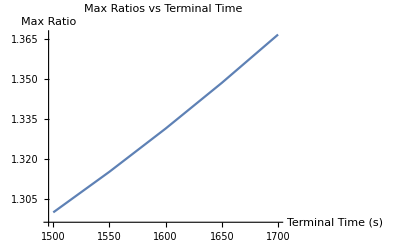

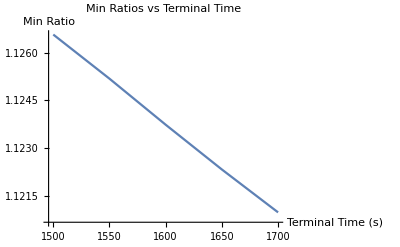

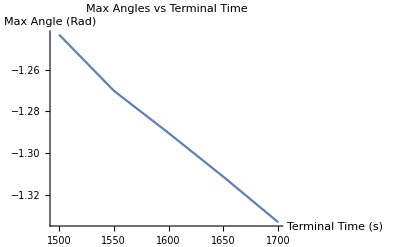

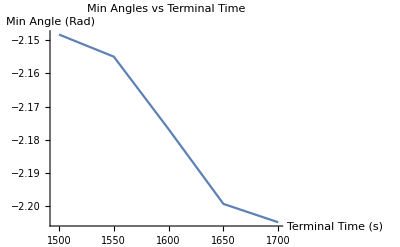

maxrat.png

minrat.png

maxangle.png

minangle.png

```mathematica
(** Plotting code **)
l1 = ListLinePlot[{terminaltimes, maxrats} // Transpose, PlotLabel -> "Max Ratios vs Terminal Time", AxesLabel-> {"Terminal Time (s)", "Max Ratio" }   ]
l2 = ListLinePlot[{terminaltimes, minrats} // Transpose, PlotLabel-> "Min Ratios vs Terminal Time", AxesLabel-> {"Terminal Time (s)", "Min Ratio" }]
l3 = ListLinePlot[{terminaltimes, maxangles} // Transpose, PlotLabel -> "Max Angles vs Terminal Time", AxesLabel-> {"Terminal Time (s)", "Max Angle (Rad)" }]
l4 = ListLinePlot[{terminaltimes, minangles} // Transpose, PlotLabel->"Min Angles vs Terminal Time", AxesLabel-> {"Terminal Time (s)", "Min Angle (Rad)"}]

Export["maxrat.png", l1]
Export["minrat.png", l2]
Export["maxangle.png", l3]
Export["minangle.png", l4]
```

```mathematica
endtime // Clear;
plotrrs[terminaltime_, quadform_, thrustmax_, n_] := Module[{testbounds, teststats},
energysetaxes[quad_] :=
Eigenvectors[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}];
energyseteigenvalues[quad_] :=  Eigenvalues[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}];
vecs = energysetaxes[quadform];
vals = energyseteigenvalues[quadform];
ax1 = vecs[[1]][[1;;2]] * ((terminaltime thrustmax^2* vals[[1]]) // Sqrt);
ax2 = vecs[[2]][[1;;2]] * ((terminaltime thrustmax^2* vals[[2]]) // Sqrt);
ax1length = Norm[ax1];
ax2length = Norm[ax2];

testbounds = thrustreachable[xrf, terminaltime, n, thrustmax];
teststats = reachablestatsoperator[quadform,testbounds, terminaltime thrustmax^2];

plot = Show[Graphics[GeometricTransformation[Circle[{0,0}, {ax1length, ax2length }], RotationTransform[ax1 // vectoangle]]], Graphics[Point[testbounds[[;;, 1 ;; 2]]]], Graphics[Arrow[ax1length AnglePath[{teststats[[2, 1]] // vectoangle}]]], Graphics[Arrow[ax2length AnglePath[{teststats[[2, 2]] // vectoangle}]]], Graphics[Text[Style["Maximum Ratio",10],ax1length (teststats[[2, 1]] // Normalize)]], Graphics[Text[Style["Minimum Ratio",10],ax2length (teststats[[2, 2]] // Normalize)]], Axes -> True, PlotLabel -> "Energy Reachable and Thrust Limited RRS"];
Export[StringForm["RRStt``.png", terminaltime] // ToString, plot]

]
```

```mathematica
(** Saving the plots **)
MapThread[plotrrs, {terminaltimes, forms, tmaxs, ns}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{RRStt1500.png,RRStt1550.png,RRStt1600.png,RRStt1650.png,RRStt1700.png}